# Sex-specific epistasis and sexual antagonism - autosomal

```mathematica
Clear["Global`*"]
```

## Haplotypes and fitness

```mathematica
haplotypes={{Af,Bf},{Af,Bm},{Am,Bf},{Am,Bm}};
```

```mathematica
wlistM={
{{Am,Am,Bm,Bm},1},
{{Af,Am,Bm,Bm},1-hAm sAm},
{{Af,Af,Bm,Bm},1-sAm},
{{Am,Am,Bf,Bm},1-hBm sBm},
{{Af,Am,Bf,Bm},(1-hAm sAm)(1-hBm sBm)+em},
{{Af,Af,Bf,Bm},(1-sAm)(1-hBm sBm)+2em},
{{Am,Am,Bf,Bf},1- sBm},
{{Af,Am,Bf,Bf},(1-hAm sAm)(1-sBm)+2em},
{{Af,Af,Bf,Bf},(1-sAm)(1-sBm)+4em}};
```

```mathematica
wlistF={
{{Am,Am,Bm,Bm},(1-sAf)(1-sBf)+4ef},
{{Af,Am,Bm,Bm},(1-hAf sAf)(1-sBf)+2 ef},
{{Af,Af,Bm,Bm},1-sBf},
{{Am,Am,Bf,Bm},(1-sAf)(1-hBf sBf)+2ef},
{{Af,Am,Bf,Bm},(1-hAf sAf)(1-hBf sBf)+ef},
{{Af,Af,Bf,Bm},1-hBf sBf},
{{Am,Am,Bf,Bf},1-sAf},
{{Af,Am,Bf,Bf},1-hAf sAf},
{{Af,Af,Bf,Bf},1}};
```

```mathematica
findW[genotype_,sex_]:=Module[{wlist,w,iter},
wlist=If[Count[{sex},f]==1,wlistF,wlistM];
w=Null;
For[iter=1,iter≤Length[wlist],iter++,
If[wlist[[iter]][[1]]==Sort[genotype],w=wlist[[iter]][[2]]]
];
Return[w]
]
```

```mathematica
Table[{Join[haplotypes[[i]],haplotypes[[j]]],findW[Join[haplotypes[[i]],haplotypes[[j]]],f]},{i,1,Length[haplotypes]},{j,1,Length[haplotypes]}]//MatrixForm
```

(({Af,Bf,Af,Bf}
1) | ({Af,Bf,Af,Bm}
1-hBf sBf) | ({Af,Bf,Am,Bf}
1-hAf sAf) | ({Af,Bf,Am,Bm}
ef+(1-hAf sAf) (1-hBf sBf))
({Af,Bm,Af,Bf}
1-hBf sBf) | ({Af,Bm,Af,Bm}
1-sBf) | ({Af,Bm,Am,Bf}
ef+(1-hAf sAf) (1-hBf sBf)) | ({Af,Bm,Am,Bm}
2 ef+(1-hAf sAf) (1-sBf))
({Am,Bf,Af,Bf}
1-hAf sAf) | ({Am,Bf,Af,Bm}
ef+(1-hAf sAf) (1-hBf sBf)) | ({Am,Bf,Am,Bf}
1-sAf) | ({Am,Bf,Am,Bm}
2 ef+(1-sAf) (1-hBf sBf))
({Am,Bm,Af,Bf}
ef+(1-hAf sAf) (1-hBf sBf)) | ({Am,Bm,Af,Bm}
2 ef+(1-hAf sAf) (1-sBf)) | ({Am,Bm,Am,Bf}
2 ef+(1-sAf) (1-hBf sBf)) | ({Am,Bm,Am,Bm}
4 ef+(1-sAf) (1-sBf)))

```mathematica
w[haploNumMom_,haploNumDad_,sex_]:=Module[{genotype,wval},(*count the total numbers of female benefit and male benefit alleles *)
genotype=Join[haplotypes[[haploNumMom]],haplotypes[[haploNumDad]]];
Return[findW[genotype,sex]]
]
```

Cross Table function

```mathematica
autosomeCross[haploNumMom_,haploNumDad_,haploNumGoal_,sex_]:=Module[{genotype,haploMom,haploDad,haploGoal,haploNoRec,haploRec},
haploMom=haplotypes[[haploNumMom]];
haploDad=haplotypes[[haploNumDad]];
haploGoal=haplotypes[[haploNumGoal]];
haploNoRec={haploMom,haploDad};
haploRec={{haploMom[[1]],haploDad[[2]]},{haploDad[[1]],haploMom[[2]]}};
Return[Simplify[Count[haploNoRec,haploGoal]/2 (1-r)+Count[haploRec,haploGoal]/2 r]]
]
```

```mathematica
autosomeCross[1,4,2,f]//Simplify
```

r/2

```mathematica
haplotypes[[2]]
```

{Af,Bm}

```mathematica
haplotypes[[3]]
```

{Am,Bf}

```mathematica
Table[autosomeCross[xi,xj,xk,f],{xi,1,4},{xj,1,4},{xk,1,4}]//MatrixForm
```

((1
0
0
0) | (1/2
1/2
0
0) | (1/2
0
1/2
0) | ((1-r)/2
r/2
r/2
(1-r)/2)
(1/2
1/2
0
0) | (0
1
0
0) | (r/2
(1-r)/2
(1-r)/2
r/2) | (0
1/2
0
1/2)
(1/2
0
1/2
0) | (r/2
(1-r)/2
(1-r)/2
r/2) | (0
0
1
0) | (0
0
1/2
1/2)
((1-r)/2
r/2
r/2
(1-r)/2) | (0
1/2
0
1/2) | (0
0
1/2
1/2) | (0
0
0
1))

## Recursions

```mathematica
ytplus1=Table[Sum[x[haploMom]y[haploDad]w[haploMom,haploDad,m]autosomeCross[haploMom,haploDad,haploGoal,m],{haploMom,1,Length[haplotypes]},{haploDad,1,Length[haplotypes]}],{haploGoal,1,Length[haplotypes]}]//Simplify;
xtplus1=Table[Sum[x[haploMom]y[haploDad]w[haploMom,haploDad,f]autosomeCross[haploMom,haploDad,haploGoal,f],{haploMom,1,Length[haplotypes]},{haploDad,1,Length[haplotypes]}],{haploGoal,1,Length[haplotypes]}]//Simplify;
```

```mathematica
wbarM=Total[ytplus1]//Simplify;
wbarF=Total[xtplus1]//Simplify;
```

```mathematica
Length[xtplus1]
```

4

```mathematica
haplotypes
```

{{Af,Bf},{Af,Bm},{Am,Bf},{Am,Bm}}

```mathematica
xtplus1/.{sAm->0,sBm->0,em->0,sBf->0,sAf->0,ef->0}//Simplify
```

{1/2 (x[3] y[1]+x[4] y[1]-r x[4] y[1]+r x[3] y[2]+x[2] (y[1]+r y[3])+x[1] (2 y[1]+y[2]+y[3]+y[4]-r y[4])),1/2 ((x[1]+x[3]+x[4]) y[2]+x[2] (y[1]+2 y[2]+y[3]-r y[3]+y[4])+r (x[4] y[1]-x[3] y[2]+x[1] y[4])),1/2 ((x[1]+x[2]+x[4]) y[3]+x[3] (y[1]+y[2]-r y[2]+2 y[3]+y[4])+r (x[4] y[1]-x[2] y[3]+x[1] y[4])),1/2 ((x[1]+x[2]+x[3]) y[4]+x[4] (y[1]-r y[1]+y[2]+y[3]+2 y[4])+r (x[3] y[2]+x[2] y[3]-x[1] y[4]))}

## Numerical iterations

```mathematica
iterate[{sAfs_,sAms_,sBfs_,sBms_},{hAfs_,hAms_,hBfs_,hBms_},{efs_,ems_},{rs_},{tend_}]:=Module[{data,xk,yk,subs,ti},
data=ConstantArray[ConstantArray[0,tend],8];
data[[All,1]]=0.25;
xk=xtplus1/wbarF/.{sAf->sAfs,sAm->sAms,sBf->sBfs,sBm->sBms,hAf->hAfs,hAm->hAms,hBf->hBfs,hBm->hBms,r->rs,ef->efs,em->ems};
yk=ytplus1/wbarM/.{sAf->sAfs,sAm->sAms,sBf->sBfs,sBm->sBms,hAf->hAfs,hAm->hAms,hBf->hBfs,hBm->hBms,r->rs,ef->efs,em->ems};
For[ti=2,ti≤tend,ti++,
subs=Flatten[Table[{x[xj]->data[[xj,ti-1]],y[xj]->data[[xj+4,ti-1]]},{xj,1,4}]];
data[[All,ti]]=Join[xk,yk]/.subs;
];
Return[data]
]
```

```mathematica
out=iterate[{0.44,0.44,0.44,0.44},{0.5,0.5,0.5,0.5},{-0.05,0.01},{0.05},{1000}];
```

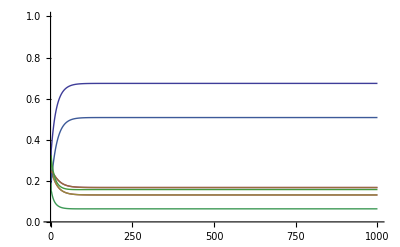

```mathematica
ListLinePlot[out,PlotRange->{0,1}]
```

```mathematica
out[[All,1000]]
```

{5.80017×10^-11,1.80211×10^-16,1.,1.76087×10^-11,1.76087×10^-11,1.80211×10^-16,1.,5.80017×10^-11}

```mathematica
haplotypes
```

{{Af,Bf},{Af,Bm},{Am,Bf},{Am,Bm}}

## Export to C

Output directory

```mathematica
directory=$HomeDirectory<>"/Projects/sex_specific_epistasis/src/numerical/autosomal/";
```

```mathematica
s2c[x_]:=ToString[CForm[x]]<>";\n\n";
```

```mathematica
str="wF = "<>s2c[wbarF];
str=str<>"wM = "<>s2c[wbarM];
For[iter=1,iter≤Length[haplotypes],iter++,
str=str<>"x"<>ToString[iter]<>"tplus1 = "<>s2c[1/wF xtplus1[[iter]]];
str=str<>"y"<>ToString[iter]<>"tplus1 = "<>s2c[1/wM ytplus1[[iter]]];
];
Export[directory<>"recursions.txt",str]
```

/home/bram/Projects/sex_specific_epistasis/src/numerical/autosomal/recursions.txt